# c.quark-flow.decompose.strongcoes.paper.ed2.nb

```mathematica
NotebookFileName[]
```

```mathematica
Quit[]
```

pre run by order:

Gen.Vertex.Dict.constituent.all

c.quark-flow.coe.nb

## note

this nb is to extract the qfa qfb values for paper use.

only consider the sea quark flow loop position, i.e. {6,2}

keep the octet mesons plain style names

initial→ quarkflow`value are the same with decompose.normal.nb

## initial

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"/expression-coes/"}]]
```

```mathematica
name`fucoeandmrrlabbr`string`normal=FileNameJoin[{Directory[],"fucoeandmrrlabbr.string.normal.m"}];
Once[fucoeandmrrlabbr`string`normal=Get[name`fucoeandmrrlabbr`string`normal]];
```

```mathematica
name`fucoeandmrrlabbr`normal=FileNameJoin[{Directory[],"fucoeandmrrlabbr.normal.m"}];
Once[fucoeandmrrlabbr`normal=Get[name`fucoeandmrrlabbr`normal]];
```

```mathematica
name`fucoeandmrrlabbr`symmetry=FileNameJoin[{Directory[],"fucoeandmrrlabbr.symmetry.m"}];
Once[fucoeandmrrlabbr`symmetry=Get[name`fucoeandmrrlabbr`symmetry]];
```

name

```mathematica
name`quarkflow`decompose`numerical=
FileNameJoin[{Directory[],"quarkflow.decompose.numerical.m"}];
name`quarkflow`decompose`symbolic=
FileNameJoin[{Directory[],"quarkflow.decompose.symbolic.m"}];
```

```mathematica
name`chqftransfer1=
FileNameJoin[{Directory[],"chpt-to-quarkflow.m"}];
name`chqftransfer2=
FileNameJoin[{Directory[],"quarkflow-to-chpt.m"}];
```

```mathematica
name`quarkflow`names=
FileNameJoin[{Directory[],"quarkflow.names.m"}];
```

get

```mathematica
Once[quarkflow`decompose`numerical=Get[name`quarkflow`decompose`numerical]];
Once[quarkflow`decompose`symbolic=Get[name`quarkflow`decompose`symbolic]];
```

```mathematica
Once[chqftransfer1=Get[name`chqftransfer1]];
Once[chqftransfer2=Get[name`chqftransfer2]];
```

```mathematica
Once[quarkflow`names=Get[name`quarkflow`names]];
```

## quench, sea, valence pick

here consider the  quarks in different position of  quarkflow diagram

so in the specialized  EM vertex in “Gen.vertex.Dict”, consider the individual contributions of individual quark

type1={1,4,5,6,7,8,9,10,11}, no flavor transition, i.e. no Σ0-Λ

type2 = {2,3},  Σ0 - Λ

type3 = {9},  octet-decuplet

```mathematica
chqftransfer1//Dimensions
chqftransfer2//Dimensions
quarkflow`decompose`symbolic//Dimensions
```

{3,5,8}

{3,5,8}

{3,5,8}

figure orders

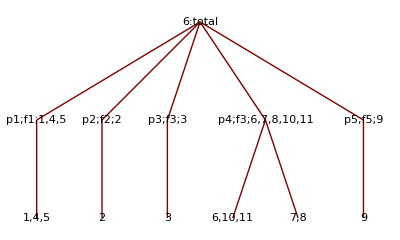

```mathematica
quarkflow`decompose`symbolic//Dimensions
fucoeandmrrlabbr`normal//Dimensions
quarkflow`names//Dimensions
chqftransfer1//Dimensions
chqftransfer2//Dimensions
```

{7,8}

{7,8}

{7,8}

«2 more identical outputs»

## order

1;1,4,5
2;2
3;3
4;6,10,11
5;7,
6;8,
7;9

fun`quarkflow`select

fun`quarkflow`select gives a list which satisfy the u/d/s/quench/sea/valence request

```mathematica
fun`quarkflow`select[quarkflow`names_,quark_,sector1_,position1_,p1p2_,sector2_,position2_]:=Select[(*quark sea loop select function gather by both "qfa" and "uubar" *)
quarkflow`names,(*all quark`flow names*)
And[
SameQ[StringTake[StringExtract[ToString[#],"`"->sector1],{position1}],quark],
SameQ[StringTake[StringExtract[ToString[#],"`"->sector2],{position2}],p1p2]
]&(* pick according to the loop quark *)
]
```

fun`paper`classify

divide the name list into qfa qfb

```mathematica
fun`paper`classify[quarkflow`names_,position_]:=GatherBy[
quarkflow`names,
StringExtract[ToString[#],"`"->position]&
];
```

extract qfa qfb

quarkflow`decompose`symbolic
fucoeandmrrlabbr`normal
quarkflow`names
chqftransfer1
chqftransfer2

classified according to the EM coupling, on mesons or baryons

## type 1 chpt figure 1,4,5; 6,10,11→1;4

fun`quarkflow`select[quarkflow`names_, quark_, sector_, position_]

fun`paper`classify[quarkflow`names_,qfa_,qfb_]

```mathematica
Once[quarkflow`decompose`total=Table[0,{flavor,1,3,1},{if,1,7,1},{io,1,8,1}]];
```

```mathematica
Once[quarkflow`decompose`seava=Table[0,{flavor,1,3,1},{if,1,7,1},{io,1,8,1}]];
```

```mathematica
Block[{quarkflow`names2},
Table[

quarkflow`names2=DeleteDuplicatesBy[
Select[(*quark sea loop select function gather by both "qfa" and "uubar" *)
quarkflow`names⟦if,io⟧,(*all quark`flow names*)
And[
SameQ[StringExtract[ToString[#],"`"->1],quark`flavor⟦flavor⟧]
]&(* pick according to the loop quark *)
],
StringExtract[ToString[#],"`"->(1;;7)]&
];(*quark position 2*)

quarkflow`decompose`total⟦flavor,if,io⟧=DeleteDuplicates[
Join[quarkflow`names2]];(*merge the quarkflow name list*)

quarkflow`decompose`seava⟦flavor,if,io⟧=GroupBy[
quarkflow`decompose`total⟦flavor,if,io⟧,
StringExtract[ToString[#],"`"->4]&
];

,{flavor,1,3,1}
,{if,1,7,1} (* figure 1 4 the same pattern *)
,{io,1,8,1}
];
];
```

## show`prepare

```mathematica
mass`replacerule={
(*octet section*)
(*"Σm"->"Σ^-","Σ0"->"Σ^0","Σp"->"Σ^+",
"Np"->"Pr","Nn"->"Ne",
"Ξm"->"Ξ^-","Ξ0"->"Ξ^0", *)
(*Λ->Λ*)
(*"uuu"->"UUU", "ddd"->"DDD", "sss"->"SSS",*)(*new vertex terms 12+7*)

(*mesons section*)
(*,"πim"->"π^-","πi0"->"π^0","πip"->"π^+",
"Κi0b"->"OverBar[K^0]",
"Κi0"->"K^0","Κim"->"K^-","Κip"->"K^+",*)
"η"->"η8"
(*,"etas"->"η0"*)

(*decuplet section*)
(*"Δm"->"Δ^-","Δ0"->"Δ^0","Δpp"->"Δ^(++)",
"Δp"->"Δ^+",
"Σsm"->"Σs^-","Σs0"->"Σs^0","Σsp"->"Σs^+",
"Ξsm"->"Ξs^-","Ξs0"->"Ξs^0",
"Ωm"->"Ω^-"*)

(*"o1"->"Σ-","o2"->"Σ0","o3"->"Σ+",
"o4"->"Pr","o5"->"Ne",
"o6"->"Ξ-","o7"->"Ξ0",*)
};
```

```mathematica
qfaqfb`replacerule={
"`qfa`"->"`sea`",
"`qfb`"->"`quench`"
(*,"ubar"->"ū","dbar"->"d̄","sbar"->"s̄"*)
};
```

## show

order: qfa (sea), qfb(quench)

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
quarkflow`seva`data[flavor_,if_,io_]:=Block[{quarkflow`seva},
quarkflow`seva=Join[
("qfa"/.quarkflow`decompose`seava⟦flavor,if,io⟧)/."qfa"->Sequence[],
("qfb"/.quarkflow`decompose`seava⟦flavor,if,io⟧)/."qfb"->Sequence[]
];
Transpose[
{
(*+++++++++++++++++++++++++++++++++++++++++++ chpt names +++++++++++++++++++++++++++++++*)
StringReplace[
StringReplace[
ToString/@(quarkflow`seva/.chqftransfer2⟦if,io⟧)
,mass`replacerule
],
qfaqfb`replacerule
],
(*+++++++++++++++++++++++++++++++++++++++++++ chpt names +++++++++++++++++++++++++++++++*)
(*+++++++++++++++++++++++++++++++++++++++++++ chpt values +++++++++++++++++++++++++++++++*)
Simplify[2 f^2*(
(quarkflow`seva/.chqftransfer2⟦if,io⟧)/.
fucoeandmrrlabbr`normal⟦if,io⟧
)
],(* chpt values *)
(*+++++++++++++++++++++++++++++++++++++++++++ chpt values +++++++++++++++++++++++++++++++*)
(*+++++++++++++++++++++++++++++++++++ quark flow names+++++++++++++++++++++ *)
StringReplace[
ToString/@quarkflow`seva,
qfaqfb`replacerule
],
(*+++++++++++++++++++++++++++++++++++ quark flow names+++++++++++++++++++++ *)
(* ++++++++++++++++++++++quark flow values +++++++++++++++++++++++++++++++++++++++++*)
Simplify[2 f^2*(
(
quarkflow`seva/.quarkflow`decompose`symbolic⟦if,io⟧
)/.fucoeandmrrlabbr`normal⟦if,io⟧
)
]
(* ++++++++++++++++++++++quark flow values +++++++++++++++++++++++++++++++++++++++++*)
}
]
]
```

if=1

## pr

total 6 figure

```mathematica
if=1;io=4;
Style[
Grid[(*grid start*)
Prepend[(*add names row*)
SortBy[(*arrange the order of table terms*)
Join[
quarkflow`seva`data[1,if,io],
quarkflow`seva`data[2,if,io],
quarkflow`seva`data[3,if,io]
]
,
{
((StringExtract[First[#],"`"->-1]/.{
"πi0"->1,"η8"->2,"η0"->3,"πip"->4,"πim"->5,"Ki0"->6,"Kip"->7
})&),(*arrange the order of table according to the chpt names: *)
((StringExtract[#⟦3⟧,"`"->1]/.{
"u"->1,"d"->2,"s"->3
})&)(*arrange the order of table according to the quark flavor names: *)
}
(*arrange the order of table according to the chpt names: *)

](*/.{di->D,fi->F,Q2->Q^2,ci->C,mo->mB,mm->mM,md->mD}*),(*add the data to display*)
{"chpt channel","chpt value","quark.flow channel","quark.flow value"}(*prepend names column *)
]
(*++++++++++only adopt the  proton neutron++++++++++++++++*)
,Frame->{All,All}
,Spacings->{1,1}
,Background->{None,{{None,None}}}
]
,FontSize->11
]
```

chpt channel | chpt value | quark.flow channel | quark.flow value
u`f1`o4`Np`Np`πi0 | 0 | u`f1`o4`sea`udu`uu`πi0`p1 | -di^2/3-fi^2
u`f1`o4`Np`Np`πi0 | 0 | u`f1`o4`quench`uud`uu`πi0`p1 | 2 f^2 u`f1`o4`fakeb`uud`uu`πi0`p1
d`f1`o4`Np`Np`πi0 | 0 | d`f1`o4`sea`duu`dd`πi0`p1 | -1/2 (di-fi)^2
u`f1`o4`Np`Np`η8 | 0 | u`f1`o4`sea`udu`uu`η`p1 | 1/9 (-di^2-3 fi^2)
u`f1`o4`Np`Np`η8 | 0 | u`f1`o4`quench`uud`uu`η`p1 | 2 f^2 u`f1`o4`fakeb`uud`uu`η`p1
d`f1`o4`Np`Np`η8 | 0 | d`f1`o4`sea`duu`dd`η`p1 | -1/6 (di-fi)^2
u`f1`o4`Np`Nn`πip | -(di+fi)^2 | u`f1`o4`sea`udu`ud`πip`p1 | -2/3 (di^2+3 fi^2)
u`f1`o4`Np`Nn`πip | -(di+fi)^2 | u`f1`o4`quench`udu`ud`πip`p1 | -di^2/3-2 di fi+fi^2
d`f1`o4`Np`Nn`πip | (di+fi)^2 | d`f1`o4`sea`udu`ud`πip`p2 | 2/3 (di^2+3 fi^2)
d`f1`o4`Np`Nn`πip | (di+fi)^2 | d`f1`o4`quench`udu`ud`πip`p2 | 1/3 (di^2+6 di fi-3 fi^2)
u`f1`o4`Np`uuu`πim | 0 | u`f1`o4`sea`duu`du`πim`p2 | (di-fi)^2
u`f1`o4`Np`uuu`πim | 0 | u`f1`o4`quench`duu`du`πim`p2 | -(di-fi)^2
d`f1`o4`Np`uuu`πim | 0 | d`f1`o4`sea`duu`du`πim`p1 | -(di-fi)^2
d`f1`o4`Np`uuu`πim | 0 | d`f1`o4`quench`duu`du`πim`p1 | (di-fi)^2
u`f1`o4`Np`Np`etas | 0 | u`f1`o4`sea`udu`uu`etas`p1 | -2/9 (di^2+3 fi^2)
u`f1`o4`Np`Np`etas | 0 | u`f1`o4`quench`uud`uu`etas`p1 | 2 f^2 u`f1`o4`fakeb`uud`uu`etas`p1
d`f1`o4`Np`Np`etas | 0 | d`f1`o4`sea`duu`dd`etas`p1 | -1/3 (di-fi)^2
d`f1`o4`Np`Σp`Κi0 | -(di-fi)^2 | d`f1`o4`sea`duu`ds`Κi0`p1 | -(di-fi)^2
s`f1`o4`Np`Σp`Κi0 | (di-fi)^2 | s`f1`o4`sea`duu`ds`Κi0`p2 | (di-fi)^2
u`f1`o4`Np`Λ`Κip + u`f1`o4`Np`Σ0`Κip | -2/3 (di^2+3 fi^2) | u`f1`o4`sea`udu`us`Κip`p1 | -2/3 (di^2+3 fi^2)
s`f1`o4`Np`Λ`Κip + s`f1`o4`Np`Σ0`Κip | 2/3 (di^2+3 fi^2) | s`f1`o4`sea`udu`us`Κip`p2 | 2/3 (di^2+3 fi^2)

```mathematica
{{"chpt channel", "chpt value", "quark.flow channel", "quark.flow value"}, {"u`f3`Np`Np`Np`πi0", -1/2 (di+fi)^2, "u`f3`sea`udu`uubar`πi0", -di^2/3-fi^2}, {"u`f3`Np`Np`Np`πi0", -1/2 (di+fi)^2, "u`f3`quench`uud`uubar`πi0", di^2/3-2 di fi+fi^2}, {"d`f3`Np`Np`Np`πi0", -1/2 (di+fi)^2, "d`f3`sea`duu`ddbar`πi0", -1/2 (di-fi)^2}, {"u`f3`Np`Np`Np`η8", -1/6 (di-3 fi)^2, "u`f3`sea`udu`uubar`η", 1/9 (-di^2-3 fi^2)}, {"u`f3`Np`Np`Np`η8", -1/6 (di-3 fi)^2, "u`f3`quench`uud`uubar`η", 1/9 (di^2+6 di fi-9 fi^2)}, {"d`f3`Np`Np`Np`η8", -1/6 (di-3 fi)^2, "d`f3`sea`duu`ddbar`η", -1/6 (di-fi)^2}, {"u`f3`Np`Np`Np`η0", 0, "u`f3`sea`udu`uubar`etas", -2/9 (di^2+3 fi^2)}, {"u`f3`Np`Np`Np`η0", 0, "u`f3`quench`uud`uubar`etas", (5 di^2)/9-(2 di fi)/3+fi^2}, {"d`f3`Np`Np`Np`η0", 0, "d`f3`sea`duu`ddbar`etas", -1/3 (di-fi)^2}, {"d`f3`Np`Nn`Nn`πip", -(di+fi)^2, "d`f3`sea`udu`udbar`πip", -2/3 (di^2+3 fi^2)}, {"d`f3`Np`Nn`Nn`πip", -(di+fi)^2, "d`f3`quench`udu`udbar`πip", -di^2/3-2 di fi+fi^2}, {"u`f3`Np`UUU`UUU`πim", 0, "u`f3`sea`duu`dubar`πim", -(di-fi)^2}, {"u`f3`Np`UUU`UUU`πim", 0, "u`f3`quench`duu`dubar`πim", (di-fi)^2}, {"s`f3`Np`Σp`Σp`Κi0", -(di-fi)^2, "s`f3`sea`duu`dsbar`Κi0", -(di-fi)^2}, {"s`f3`Np`Λ`Λ`Κip + s`f3`Np`Λ`Σ0`Κip + s`f3`Np`Σ0`Λ`Κip + s`f3`Np`Σ0`Σ0`Κip", 1/3 ((-2+√3) di^2+2 √3 di fi-3 (2+√3) fi^2), "s`f3`sea`udu`usbar`Κip", -2/3 (di^2+3 fi^2)}}
```

## ne

```mathematica
if=3;io=5;
Style[
Grid[(*grid start*)
Prepend[(*add names row*)
SortBy[(*arrange the order of table terms*)
Join[
quarkflow`seva`data[1,if,io],
quarkflow`seva`data[2,if,io],
quarkflow`seva`data[3,if,io]
]
,
{
((StringExtract[First[#],"`"->-1]/.{
"πi0"->1,"η8"->2,"η0"->3,"πip"->4,"πim"->5,"Ki0"->6,"Kip"->7
})&),(*arrange the order of table according to the chpt names: *)
((StringExtract[#⟦3⟧,"`"->1]/.{
"u"->1,"d"->2,"s"->3
})&)(*arrange the order of table according to the quark flavor names: *)
}
(*arrange the order of table according to the chpt names: *)

](*/.{di->D,fi->F,Q2->Q^2,ci->C,mo->mB,mm->mM,md->mD}*),(*add the data to display*)
{"chpt channel","chpt value","quark.flow channel","quark.flow value"}(*prepend names column *)
]
(*++++++++++only adopt the  proton neutron++++++++++++++++*)
,Frame->{All,All}
,Spacings->{1,1}
,Background->{None,{{None,None}}}
]
,FontSize->12
]
```

chpt channel | chpt value | quark.flow channel | quark.flow value
u`f3`Nn`Nn`Nn`πi0 | -1/2 (di+fi)^2 | u`f3`sea`udd`uubar`πi0 | -1/2 (di-fi)^2
d`f3`Nn`Nn`Nn`πi0 | -1/2 (di+fi)^2 | d`f3`sea`ddu`ddbar`πi0 | -di^2/3-fi^2
d`f3`Nn`Nn`Nn`πi0 | -1/2 (di+fi)^2 | d`f3`quench`ddu`ddbar`πi0 | di^2/3-2 di fi+fi^2
u`f3`Nn`Nn`Nn`η8 | -1/6 (di-3 fi)^2 | u`f3`sea`udd`uubar`η | -1/6 (di-fi)^2
d`f3`Nn`Nn`Nn`η8 | -1/6 (di-3 fi)^2 | d`f3`sea`ddu`ddbar`η | 1/9 (-di^2-3 fi^2)
d`f3`Nn`Nn`Nn`η8 | -1/6 (di-3 fi)^2 | d`f3`quench`ddu`ddbar`η | 1/9 (di^2+6 di fi-9 fi^2)
u`f3`Nn`Nn`Nn`η0 | 0 | u`f3`sea`udd`uubar`etas | -1/3 (di-fi)^2
d`f3`Nn`Nn`Nn`η0 | 0 | d`f3`sea`ddu`ddbar`etas | -2/9 (di^2+3 fi^2)
d`f3`Nn`Nn`Nn`η0 | 0 | d`f3`quench`ddu`ddbar`etas | (5 di^2)/9-(2 di fi)/3+fi^2
d`f3`Nn`DDD`DDD`πip | 0 | d`f3`sea`udd`udbar`πip | -(di-fi)^2
d`f3`Nn`DDD`DDD`πip | 0 | d`f3`quench`udd`udbar`πip | (di-fi)^2
u`f3`Nn`Np`Np`πim | -(di+fi)^2 | u`f3`sea`ddu`dubar`πim | -2/3 (di^2+3 fi^2)
u`f3`Nn`Np`Np`πim | -(di+fi)^2 | u`f3`quench`dud`dubar`πim | -di^2/3-2 di fi+fi^2
s`f3`Nn`Λ`Λ`Κi0 + s`f3`Nn`Λ`Σ0`Κi0 + s`f3`Nn`Σ0`Λ`Κi0 + s`f3`Nn`Σ0`Σ0`Κi0 | -1/3 (2+√3) di^2-(2 di fi)/(√3)+(-2+√3) fi^2 | s`f3`sea`ddu`dsbar`Κi0 | -2/3 (di^2+3 fi^2)
s`f3`Nn`Σm`Σm`Κip | -(di-fi)^2 | s`f3`sea`udd`usbar`Κip | -(di-fi)^2

if=3

## pr

total 6 figure

```mathematica
if=3;io=4;
Style[
Grid[(*grid start*)
Prepend[(*add names row*)
SortBy[(*arrange the order of table terms*)
Join[
quarkflow`seva`data[1,if,io],
quarkflow`seva`data[2,if,io],
quarkflow`seva`data[3,if,io]
]
,
{
((StringExtract[First[#],"`"->-1]/.{
"πi0"->1,"η8"->2,"η0"->3,"πip"->4,"πim"->5,"Ki0"->6,"Kip"->7
})&),(*arrange the order of table according to the chpt names: *)
((StringExtract[#⟦3⟧,"`"->1]/.{
"u"->1,"d"->2,"s"->3
})&)(*arrange the order of table according to the quark flavor names: *)
}
(*arrange the order of table according to the chpt names: *)

](*/.{di->D,fi->F,Q2->Q^2,ci->C,mo->mB,mm->mM,md->mD}*),(*add the data to display*)
{"chpt channel","chpt value","quark.flow channel","quark.flow value"}(*prepend names column *)
]
(*++++++++++only adopt the  proton neutron++++++++++++++++*)
,Frame->{All,All}
,Spacings->{1,1}
,Background->{None,{{None,None}}}
]
,FontSize->11
]
```

Transpose::nmtx: {{{{}, {}, {}, {}, {}, {}},{{}, {}, {}, {}, {}, {}},{{}, {}, {}, {}, {}, {}},{{}, {}, {}, {}, {}, {}},{{}, {}, {}, {}, {}, {}},{{}, {}, {}, {}, {}, {}},{{}, {}, {}, {}, {}, {}}},{{{{{},{},{},{},{},{}},«6»},{«1»},«3»,{«1»}},«6»},{},{{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}}}} 的前两层无法转置.

Join::heads: 位置 1 和 2 处的头部 List 和 Transpose 应该是一样的.

StringExtract::strse: «1» 的位置 1 处应该是字符串或者由字符串组成的列表.

StringExtract::strse: StringExtract[{{{{}, {}, {}, {}, {}, {}},{{}, {}, {}, {}, {}, {}},{{}, {}, {}, {}, {}, {}},{{}, {}, {}, {}, {}, {}},{{}, {}, {}, {}, {}, {}},{{}, {}, {}, {}, {}, {}},{{}, {}, {}, {}, {}, {}}},{«1»},{},{{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}},{{},{},{},{},{},{}}}},`→-1] 的位置 1 处应该是字符串或者由字符串组成的列表.

General::stop: 在本次计算中，StringExtract::strse 的进一步输出将被抑制.

$Aborted

```mathematica
{{"chpt channel", "chpt value", "quark.flow channel", "quark.flow value"}, {"u`f3`Np`Np`Np`πi0", -1/2 (di+fi)^2, "u`f3`sea`udu`uubar`πi0", -di^2/3-fi^2}, {"u`f3`Np`Np`Np`πi0", -1/2 (di+fi)^2, "u`f3`quench`uud`uubar`πi0", di^2/3-2 di fi+fi^2}, {"d`f3`Np`Np`Np`πi0", -1/2 (di+fi)^2, "d`f3`sea`duu`ddbar`πi0", -1/2 (di-fi)^2}, {"u`f3`Np`Np`Np`η8", -1/6 (di-3 fi)^2, "u`f3`sea`udu`uubar`η", 1/9 (-di^2-3 fi^2)}, {"u`f3`Np`Np`Np`η8", -1/6 (di-3 fi)^2, "u`f3`quench`uud`uubar`η", 1/9 (di^2+6 di fi-9 fi^2)}, {"d`f3`Np`Np`Np`η8", -1/6 (di-3 fi)^2, "d`f3`sea`duu`ddbar`η", -1/6 (di-fi)^2}, {"u`f3`Np`Np`Np`η0", 0, "u`f3`sea`udu`uubar`etas", -2/9 (di^2+3 fi^2)}, {"u`f3`Np`Np`Np`η0", 0, "u`f3`quench`uud`uubar`etas", (5 di^2)/9-(2 di fi)/3+fi^2}, {"d`f3`Np`Np`Np`η0", 0, "d`f3`sea`duu`ddbar`etas", -1/3 (di-fi)^2}, {"d`f3`Np`Nn`Nn`πip", -(di+fi)^2, "d`f3`sea`udu`udbar`πip", -2/3 (di^2+3 fi^2)}, {"d`f3`Np`Nn`Nn`πip", -(di+fi)^2, "d`f3`quench`udu`udbar`πip", -di^2/3-2 di fi+fi^2}, {"u`f3`Np`UUU`UUU`πim", 0, "u`f3`sea`duu`dubar`πim", -(di-fi)^2}, {"u`f3`Np`UUU`UUU`πim", 0, "u`f3`quench`duu`dubar`πim", (di-fi)^2}, {"s`f3`Np`Σp`Σp`Κi0", -(di-fi)^2, "s`f3`sea`duu`dsbar`Κi0", -(di-fi)^2}, {"s`f3`Np`Λ`Λ`Κip + s`f3`Np`Λ`Σ0`Κip + s`f3`Np`Σ0`Λ`Κip + s`f3`Np`Σ0`Σ0`Κip", 1/3 ((-2+√3) di^2+2 √3 di fi-3 (2+√3) fi^2), "s`f3`sea`udu`usbar`Κip", -2/3 (di^2+3 fi^2)}}
```

## ne

```mathematica
if=3;io=5;
Style[
Grid[(*grid start*)
Prepend[(*add names row*)
SortBy[(*arrange the order of table terms*)
Join[
quarkflow`seva`data[1,if,io],
quarkflow`seva`data[2,if,io],
quarkflow`seva`data[3,if,io]
]
,
{
((StringExtract[First[#],"`"->-1]/.{
"πi0"->1,"η8"->2,"η0"->3,"πip"->4,"πim"->5,"Ki0"->6,"Kip"->7
})&),(*arrange the order of table according to the chpt names: *)
((StringExtract[#⟦3⟧,"`"->1]/.{
"u"->1,"d"->2,"s"->3
})&)(*arrange the order of table according to the quark flavor names: *)
}
(*arrange the order of table according to the chpt names: *)

](*/.{di->D,fi->F,Q2->Q^2,ci->C,mo->mB,mm->mM,md->mD}*),(*add the data to display*)
{"chpt channel","chpt value","quark.flow channel","quark.flow value"}(*prepend names column *)
]
(*++++++++++only adopt the  proton neutron++++++++++++++++*)
,Frame->{All,All}
,Spacings->{1,1}
,Background->{None,{{None,None}}}
]
,FontSize->12
]
```

chpt channel | chpt value | quark.flow channel | quark.flow value
u`f3`Nn`Nn`Nn`πi0 | -1/2 (di+fi)^2 | u`f3`sea`udd`uubar`πi0 | -1/2 (di-fi)^2
d`f3`Nn`Nn`Nn`πi0 | -1/2 (di+fi)^2 | d`f3`sea`ddu`ddbar`πi0 | -di^2/3-fi^2
d`f3`Nn`Nn`Nn`πi0 | -1/2 (di+fi)^2 | d`f3`quench`ddu`ddbar`πi0 | di^2/3-2 di fi+fi^2
u`f3`Nn`Nn`Nn`η8 | -1/6 (di-3 fi)^2 | u`f3`sea`udd`uubar`η | -1/6 (di-fi)^2
d`f3`Nn`Nn`Nn`η8 | -1/6 (di-3 fi)^2 | d`f3`sea`ddu`ddbar`η | 1/9 (-di^2-3 fi^2)
d`f3`Nn`Nn`Nn`η8 | -1/6 (di-3 fi)^2 | d`f3`quench`ddu`ddbar`η | 1/9 (di^2+6 di fi-9 fi^2)
u`f3`Nn`Nn`Nn`η0 | 0 | u`f3`sea`udd`uubar`etas | -1/3 (di-fi)^2
d`f3`Nn`Nn`Nn`η0 | 0 | d`f3`sea`ddu`ddbar`etas | -2/9 (di^2+3 fi^2)
d`f3`Nn`Nn`Nn`η0 | 0 | d`f3`quench`ddu`ddbar`etas | (5 di^2)/9-(2 di fi)/3+fi^2
d`f3`Nn`DDD`DDD`πip | 0 | d`f3`sea`udd`udbar`πip | -(di-fi)^2
d`f3`Nn`DDD`DDD`πip | 0 | d`f3`quench`udd`udbar`πip | (di-fi)^2
u`f3`Nn`Np`Np`πim | -(di+fi)^2 | u`f3`sea`ddu`dubar`πim | -2/3 (di^2+3 fi^2)
u`f3`Nn`Np`Np`πim | -(di+fi)^2 | u`f3`quench`dud`dubar`πim | -di^2/3-2 di fi+fi^2
s`f3`Nn`Λ`Λ`Κi0 + s`f3`Nn`Λ`Σ0`Κi0 + s`f3`Nn`Σ0`Λ`Κi0 + s`f3`Nn`Σ0`Σ0`Κi0 | -1/3 (2+√3) di^2-(2 di fi)/(√3)+(-2+√3) fi^2 | s`f3`sea`ddu`dsbar`Κi0 | -2/3 (di^2+3 fi^2)
s`f3`Nn`Σm`Σm`Κip | -(di-fi)^2 | s`f3`sea`udd`usbar`Κip | -(di-fi)^2

if=6

## pr

total 6 figure

```mathematica
if=6;io=4;
Style[
Grid[(*grid start*)
Prepend[(*add names row*)
SortBy[(*arrange the order of table terms*)
Join[
quarkflow`seva`data[1,if,io],
quarkflow`seva`data[2,if,io],
quarkflow`seva`data[3,if,io]
]
,
{
((StringExtract[First[#],"`"->-1]/.{
"πi0"->1,"η8"->2,"η0"->3,"πip"->4,"πim"->5,"Ki0"->6,"Kip"->7
})&),(*arrange the order of table according to the chpt names: *)
((StringExtract[#⟦3⟧,"`"->1]/.{
"u"->1,"d"->2,"s"->3
})&)(*arrange the order of table according to the quark flavor names: *)
}
(*arrange the order of table according to the chpt names: *)

](*/.{di->D,fi->F,Q2->Q^2,ci->C,mo->mB,mm->mM,md->mD}*),(*add the data to display*)
{"chpt channel","chpt value","quark.flow channel","quark.flow value"}(*prepend names column *)
]
(*++++++++++only adopt the  proton neutron++++++++++++++++*)
,Frame->{All,All}
,Spacings->{1,1}
,Background->{None,{{None,None}}}
]
,FontSize->11
]
```

```mathematica
{{"chpt channel", "chpt value", "quark.flow channel", "quark.flow value"}, {"u`f5`Np`Δp`Np`πi0", (ci (di+fi))/(√3), "u`f5`sea`udu`uubar`πi0", (ci (-di+fi))/(2 √3)}, {"u`f5`Np`Δp`Np`πi0", (ci (di+fi))/(√3), "u`f5`quench`uud`uubar`πi0", (ci (5 di-fi))/(2 √3)}, {"d`f5`Np`Δp`Np`πi0", (ci (di+fi))/(√3), "d`f5`sea`duu`ddbar`πi0", (ci (di-fi))/(√3)}, {"d`f5`Np`Δ0`Nn`πip", (ci (di+fi))/(√3), "d`f5`sea`udu`udbar`πip", (ci (di-fi))/(√3)}, {"d`f5`Np`Δ0`Nn`πip", (ci (di+fi))/(√3), "d`f5`quench`udu`udbar`πip", (2 ci fi)/(√3)}, {"u`f5`Np`Δpp`UUU`πim", 0, "u`f5`sea`duu`dubar`πim", (ci (di-fi))/(√3)}, {"u`f5`Np`Δpp`UUU`πim", 0, "u`f5`quench`duu`dubar`πim", (ci (-di+fi))/(√3)}, {"s`f5`Np`Σsp`Σp`Κi0", (ci (-di+fi))/(√3), "s`f5`sea`duu`dsbar`Κi0", (ci (-di+fi))/(√3)}, {"s`f5`Np`Σs0`Λ`Κip + s`f5`Np`Σs0`Σ0`Κip", 1/6 ci ((-1+√3) di-(3+√3) fi), "s`f5`sea`udu`usbar`Κip", (ci (di-fi))/(2 √3)}}
```

## ne

```mathematica
if=6;io=5;
Style[
Grid[(*grid start*)
Prepend[(*add names row*)
SortBy[(*arrange the order of table terms*)
Join[
quarkflow`seva`data[1,if,io],
quarkflow`seva`data[2,if,io],
quarkflow`seva`data[3,if,io]
]
,
{
((StringExtract[First[#],"`"->-1]/.{
"πi0"->1,"η8"->2,"η0"->3,"πip"->4,"πim"->5,"Ki0"->6,"Kip"->7
})&),(*arrange the order of table according to the chpt names: *)
((StringExtract[#⟦3⟧,"`"->1]/.{
"u"->1,"d"->2,"s"->3
})&)(*arrange the order of table according to the quark flavor names: *)
}
(*arrange the order of table according to the chpt names: *)

](*/.{di->D,fi->F,Q2->Q^2,ci->C,mo->mB,mm->mM,md->mD}*),(*add the data to display*)
{"chpt channel","chpt value","quark.flow channel","quark.flow value"}(*prepend names column *)
]
(*++++++++++only adopt the  proton neutron++++++++++++++++*)
,Frame->{All,All}
,Spacings->{1,1}
,Background->{None,{{None,None}}}
]
,FontSize->12
]
```

chpt channel | chpt value | quark.flow channel | quark.flow value
u`f5`Nn`Δ0`Nn`πi0 | -(ci (di+fi))/(√3) | u`f5`sea`udd`uubar`πi0 | (ci (-di+fi))/(√3)
d`f5`Nn`Δ0`Nn`πi0 | -(ci (di+fi))/(√3) | d`f5`sea`ddu`ddbar`πi0 | (ci (di-fi))/(√3)
d`f5`Nn`Δ0`Nn`πi0 | -(ci (di+fi))/(√3) | d`f5`quench`ddu`ddbar`πi0 | (ci (-3 di+fi))/(√3)
d`f5`Nn`Δm`DDD`πip | 0 | d`f5`sea`udd`udbar`πip | (ci (-di+fi))/(√3)
d`f5`Nn`Δm`DDD`πip | 0 | d`f5`quench`udd`udbar`πip | (ci (di-fi))/(√3)
u`f5`Nn`Δp`Np`πim | -(ci (di+fi))/(√3) | u`f5`sea`ddu`dubar`πim | (ci (-di+fi))/(√3)
u`f5`Nn`Δp`Np`πim | -(ci (di+fi))/(√3) | u`f5`quench`dud`dubar`πim | -(2 ci fi)/(√3)
s`f5`Nn`Σs0`Λ`Κi0 + s`f5`Nn`Σs0`Σ0`Κi0 | 1/6 ci (di+√3 di+3 fi-√3 fi) | s`f5`sea`ddu`dsbar`Κi0 | (ci (di-fi))/(2 √3)
s`f5`Nn`Σsm`Σm`Κip | (ci (di-fi))/(√3) | s`f5`sea`udd`usbar`Κip | (ci (di-fi))/(√3)